```mathematica
<<FormsAndVectors`
SetOptions[Simplify,Trig->False]
```

{Assumptions:>$Assumptions,ComplexityFunction→Automatic,ExcludedForms→{},TimeConstraint→300,TransformationFunctions→Automatic,Trig→False}

```mathematica
gG={{g11[u,v],g12[u,v]},{g12[u,v],g22[u,v]}};
gI = {{1,0},{0,1}};
gS={{1,0},{0,Sin[u]^2}};
cx=1
cy=1
cz=2
gE={{cz^2 Sin[u]^2+Cos[u]^2 (cx^2 Cos[v]^2+cy^2 Sin[v]^2),(-cx^2+cy^2) Cos[u] Cos[v] Sin[u] Sin[v]},{(-cx^2+cy^2) Cos[u] Cos[v] Sin[u] Sin[v],Sin[u]^2 (cy^2 Cos[v]^2+cx^2 Sin[v]^2)}};
g=gG
$Assumptions=Det[g]>0
(*$Assumptions=Det[g]>0 && u >0&&u <π&&v>0&&v<2π*)
vol=Sqrt[Det[g]]//Simplify
gInv = Inverse[g]//Simplify
LC=vol*LeviCivitaTensor[2]//Normal
K=GaussCurvFromMetric[u,v,g]//Simplify
B={{B11[u,v],B12[u,v]},{B12[u,v],B22[u,v]}};
B=(B/.(Solve[Det[B.gInv]==K,B12[u,v]][[1]]//Simplify)[[1]]//Simplify)//Simplify
H=Tr[B.gInv]//Simplify
```

1

1

2

{{g11[u,v],g12[u,v]},{g12[u,v],g22[u,v]}}

-g12[u,v]^2+g11[u,v] g22[u,v]>0

√(-g12[u,v]^2+g11[u,v] g22[u,v])

{{g22[u,v]/(-g12[u,v]^2+g11[u,v] g22[u,v]),g12[u,v]/(g12[u,v]^2-g11[u,v] g22[u,v])},{g12[u,v]/(g12[u,v]^2-g11[u,v] g22[u,v]),g11[u,v]/(-g12[u,v]^2+g11[u,v] g22[u,v])}}

{{0,√(-g12[u,v]^2+g11[u,v] g22[u,v])},{-√(-g12[u,v]^2+g11[u,v] g22[u,v]),0}}

1/(4 (g12[u,v]^2-g11[u,v] g22[u,v])^2)(g11[u,v] (g11^(0,1)[u,v] g22^(0,1)[u,v]-2 g22^(0,1)[u,v] g12^(1,0)[u,v]+(g22^(1,0)[u,v])^2)+g12[u,v] (g22^(0,1)[u,v] g11^(1,0)[u,v]+2 g12^(1,0)[u,v] (2 g12^(0,1)[u,v]-g22^(1,0)[u,v])-g11^(0,1)[u,v] (2 g12^(0,1)[u,v]+g22^(1,0)[u,v]))+2 g12[u,v]^2 (g11^(0,2)[u,v]-2 g12^(1,1)[u,v]+g22^(2,0)[u,v])+g22[u,v] ((g11^(0,1)[u,v])^2+g11^(1,0)[u,v] (-2 g12^(0,1)[u,v]+g22^(1,0)[u,v])-2 g11[u,v] (g11^(0,2)[u,v]-2 g12^(1,1)[u,v]+g22^(2,0)[u,v])))

{{B11[u,v],-1/(2 √(g12[u,v]^2-g11[u,v] g22[u,v]))(√(4 B11[u,v] B22[u,v] (g12[u,v]^2-g11[u,v] g22[u,v])-2 g12[u,v] g11^(0,1)[u,v] g12^(0,1)[u,v]+g11[u,v] g11^(0,1)[u,v] g22^(0,1)[u,v]+2 g12[u,v]^2 g11^(0,2)[u,v]+g12[u,v] g22^(0,1)[u,v] g11^(1,0)[u,v]+4 g12[u,v] g12^(0,1)[u,v] g12^(1,0)[u,v]-2 g11[u,v] g22^(0,1)[u,v] g12^(1,0)[u,v]-g12[u,v] g11^(0,1)[u,v] g22^(1,0)[u,v]-2 g12[u,v] g12^(1,0)[u,v] g22^(1,0)[u,v]+g11[u,v] (g22^(1,0)[u,v])^2-4 g12[u,v]^2 g12^(1,1)[u,v]+2 g12[u,v]^2 g22^(2,0)[u,v]+g22[u,v] ((g11^(0,1)[u,v])^2+g11^(1,0)[u,v] (-2 g12^(0,1)[u,v]+g22^(1,0)[u,v])-2 g11[u,v] (g11^(0,2)[u,v]-2 g12^(1,1)[u,v]+g22^(2,0)[u,v]))))},{-1/(2 √(g12[u,v]^2-g11[u,v] g22[u,v]))(√(4 B11[u,v] B22[u,v] (g12[u,v]^2-g11[u,v] g22[u,v])-2 g12[u,v] g11^(0,1)[u,v] g12^(0,1)[u,v]+g11[u,v] g11^(0,1)[u,v] g22^(0,1)[u,v]+2 g12[u,v]^2 g11^(0,2)[u,v]+g12[u,v] g22^(0,1)[u,v] g11^(1,0)[u,v]+4 g12[u,v] g12^(0,1)[u,v] g12^(1,0)[u,v]-2 g11[u,v] g22^(0,1)[u,v] g12^(1,0)[u,v]-g12[u,v] g11^(0,1)[u,v] g22^(1,0)[u,v]-2 g12[u,v] g12^(1,0)[u,v] g22^(1,0)[u,v]+g11[u,v] (g22^(1,0)[u,v])^2-4 g12[u,v]^2 g12^(1,1)[u,v]+2 g12[u,v]^2 g22^(2,0)[u,v]+g22[u,v] ((g11^(0,1)[u,v])^2+g11^(1,0)[u,v] (-2 g12^(0,1)[u,v]+g22^(1,0)[u,v])-2 g11[u,v] (g11^(0,2)[u,v]-2 g12^(1,1)[u,v]+g22^(2,0)[u,v])))),B22[u,v]}}

(B22[u,v] g11[u,v])/(-g12[u,v]^2+g11[u,v] g22[u,v])+(B11[u,v] g22[u,v])/(-g12[u,v]^2+g11[u,v] g22[u,v])-1/((g12[u,v]^2-g11[u,v] g22[u,v])^(3/2))g12[u,v] √(4 B11[u,v] B22[u,v] (g12[u,v]^2-g11[u,v] g22[u,v])-2 g12[u,v] g11^(0,1)[u,v] g12^(0,1)[u,v]+g11[u,v] g11^(0,1)[u,v] g22^(0,1)[u,v]+2 g12[u,v]^2 g11^(0,2)[u,v]+g12[u,v] g22^(0,1)[u,v] g11^(1,0)[u,v]+4 g12[u,v] g12^(0,1)[u,v] g12^(1,0)[u,v]-2 g11[u,v] g22^(0,1)[u,v] g12^(1,0)[u,v]-g12[u,v] g11^(0,1)[u,v] g22^(1,0)[u,v]-2 g12[u,v] g12^(1,0)[u,v] g22^(1,0)[u,v]+g11[u,v] (g22^(1,0)[u,v])^2-4 g12[u,v]^2 g12^(1,1)[u,v]+2 g12[u,v]^2 g22^(2,0)[u,v]+g22[u,v] ((g11^(0,1)[u,v])^2+g11^(1,0)[u,v] (-2 g12^(0,1)[u,v]+g22^(1,0)[u,v])-2 g11[u,v] (g11^(0,2)[u,v]-2 g12^(1,1)[u,v]+g22^(2,0)[u,v])))

```mathematica
F=(Outer[Times,g,g]+Outer[Times,LC,LC])/2//Simplify;
p={pu[u,v],pv[u,v]};
q=p.gInv.F.gInv.p//Simplify
q-Transpose[q]//Simplify
Tr[q.gInv]//Simplify
```

{{(2 g12[u,v]^2 pu[u,v]^2-g11[u,v] g22[u,v] pu[u,v]^2-2 g11[u,v] g12[u,v] pu[u,v] pv[u,v]+g11[u,v]^2 pv[u,v]^2)/(2 g12[u,v]^2-2 g11[u,v] g22[u,v]),(g12[u,v] g22[u,v] pu[u,v]^2-2 g11[u,v] g22[u,v] pu[u,v] pv[u,v]+g11[u,v] g12[u,v] pv[u,v]^2)/(2 g12[u,v]^2-2 g11[u,v] g22[u,v])},{(g12[u,v] g22[u,v] pu[u,v]^2-2 g11[u,v] g22[u,v] pu[u,v] pv[u,v]+g11[u,v] g12[u,v] pv[u,v]^2)/(2 g12[u,v]^2-2 g11[u,v] g22[u,v]),(-g22[u,v]^2 pu[u,v]^2-2 g12[u,v]^2 pv[u,v]^2+g22[u,v] pv[u,v] (2 g12[u,v] pu[u,v]+g11[u,v] pv[u,v]))/(-2 g12[u,v]^2+2 g11[u,v] g22[u,v])}}

{{0,0},{0,0}}

0

```mathematica
hp=Hodge1[p,g]//Simplify
n2p=p.gInv.p//Simplify
q.gInv.p-(n2p/2)*p//Simplify
q.gInv.hp+(n2p/2)*hp//Simplify
```

{(g12[u,v] pu[u,v]-g11[u,v] pv[u,v])/(√(-g12[u,v]^2+g11[u,v] g22[u,v])),(g22[u,v] pu[u,v]-g12[u,v] pv[u,v])/(√(-g12[u,v]^2+g11[u,v] g22[u,v]))}

(g22[u,v] pu[u,v]^2+pv[u,v] (-2 g12[u,v] pu[u,v]+g11[u,v] pv[u,v]))/(-g12[u,v]^2+g11[u,v] g22[u,v])

{0,0}

{0,0}

```mathematica
CDq=CoDFFTensor[q,u,v,g]//Simplify
CDp=CoDForm1[p,u,v,g]//Simplify
CDq-2*p.gInv.F.gInv.CDp//Simplify
```

{{{1/(2 (g12[u,v]^2-g11[u,v] g22[u,v])^2)(4 g12[u,v]^4 pu[u,v] pu^(1,0)[u,v]+g12[u,v]^2 (2 g22[u,v] pu[u,v]^2 g11^(1,0)[u,v]+g11[u,v] (pv[u,v]^2 g11^(1,0)[u,v]+pu[u,v]^2 g22^(1,0)[u,v]-2 pu[u,v] (pv[u,v] (g11^(0,1)[u,v]-3 g12^(1,0)[u,v])+3 g22[u,v] pu^(1,0)[u,v]))+2 g11[u,v]^2 pv[u,v] pv^(1,0)[u,v])+2 g12[u,v]^3 (pu[u,v]^2 (g11^(0,1)[u,v]-2 g12^(1,0)[u,v])-g11[u,v] pv[u,v] pu^(1,0)[u,v]-pu[u,v] (pv[u,v] g11^(1,0)[u,v]+g11[u,v] pv^(1,0)[u,v]))+g11[u,v] (-g22[u,v]^2 pu[u,v]^2 g11^(1,0)[u,v]+2 g11[u,v] g22[u,v] pu[u,v] (pv[u,v] (g11^(0,1)[u,v]-g12^(1,0)[u,v])+g22[u,v] pu^(1,0)[u,v])+g11[u,v]^2 pv[u,v] (pv[u,v] g22^(1,0)[u,v]-2 g22[u,v] pv^(1,0)[u,v]))+2 g11[u,v] g12[u,v] (-g11[u,v] pv[u,v] (pv[u,v] g12^(1,0)[u,v]+pu[u,v] g22^(1,0)[u,v])+g22[u,v] (pu[u,v]^2 (-g11^(0,1)[u,v]+g12^(1,0)[u,v])+g11[u,v] pv[u,v] pu^(1,0)[u,v]+g11[u,v] pu[u,v] pv^(1,0)[u,v]))),1/(2 (g12[u,v]^2-g11[u,v] g22[u,v])^2)(4 g12[u,v]^4 pu[u,v] pu^(0,1)[u,v]-2 g12[u,v]^3 (g11[u,v] pv[u,v] pu^(0,1)[u,v]+pu[u,v] (pv[u,v] g11^(0,1)[u,v]+g11[u,v] pv^(0,1)[u,v])+pu[u,v]^2 g22^(1,0)[u,v])+g11[u,v] (g11[u,v]^2 pv[u,v]^2 g22^(0,1)[u,v]+g22[u,v]^2 pu[u,v] (-pu[u,v] g11^(0,1)[u,v]+2 g11[u,v] pu^(0,1)[u,v])-2 g11[u,v] g22[u,v] pv[u,v] (g11[u,v] pv^(0,1)[u,v]+pu[u,v] (-g12^(0,1)[u,v]+g22^(1,0)[u,v])))+2 g11[u,v] g12[u,v] (-g11[u,v] pv[u,v] (pv[u,v] g12^(0,1)[u,v]+pu[u,v] g22^(0,1)[u,v])+g22[u,v] (g11[u,v] pv[u,v] pu^(0,1)[u,v]+g11[u,v] pu[u,v] pv^(0,1)[u,v]+pu[u,v]^2 (-g12^(0,1)[u,v]+g22^(1,0)[u,v])))+g12[u,v]^2 (2 g22[u,v] pu[u,v] (pu[u,v] g11^(0,1)[u,v]-3 g11[u,v] pu^(0,1)[u,v])+g11[u,v] (pv[u,v]^2 g11^(0,1)[u,v]+pu[u,v]^2 g22^(0,1)[u,v]+2 pv[u,v] (g11[u,v] pv^(0,1)[u,v]+pu[u,v] (g12^(0,1)[u,v]+g22^(1,0)[u,v])))))},{1/(2 (g12[u,v]^2-g11[u,v] g22[u,v])^2)(2 g12[u,v]^3 (g22[u,v] pu[u,v] pu^(1,0)[u,v]+g11[u,v] pv[u,v] pv^(1,0)[u,v])+g11[u,v] g22[u,v] (g11[u,v] pv[u,v] (pv[u,v] (g11^(0,1)[u,v]-2 g12^(1,0)[u,v])-pu[u,v] g22^(1,0)[u,v])-g22[u,v] (pu[u,v]^2 g11^(0,1)[u,v]-2 g11[u,v] pv[u,v] pu^(1,0)[u,v]+pu[u,v] (pv[u,v] g11^(1,0)[u,v]-2 g11[u,v] pv^(1,0)[u,v])))+g12[u,v] (g11[u,v]^2 pv[u,v]^2 g22^(1,0)[u,v]+g22[u,v]^2 pu[u,v] (pu[u,v] g11^(1,0)[u,v]-2 g11[u,v] pu^(1,0)[u,v])+g11[u,v] g22[u,v] (pv[u,v]^2 g11^(1,0)[u,v]+pu[u,v]^2 g22^(1,0)[u,v]+pv[u,v] (4 pu[u,v] g12^(1,0)[u,v]-2 g11[u,v] pv^(1,0)[u,v])))+g12[u,v]^2 (-g11[u,v] pv[u,v] (pv[u,v] g11^(0,1)[u,v]+pu[u,v] g22^(1,0)[u,v])+g22[u,v] (pu[u,v]^2 (g11^(0,1)[u,v]-2 g12^(1,0)[u,v])-2 g11[u,v] pv[u,v] pu^(1,0)[u,v]-pu[u,v] (pv[u,v] g11^(1,0)[u,v]+2 g11[u,v] pv^(1,0)[u,v])))),1/(2 (g12[u,v]^2-g11[u,v] g22[u,v])^2)(2 g12[u,v]^3 (g22[u,v] pu[u,v] pu^(0,1)[u,v]+g11[u,v] pv[u,v] pv^(0,1)[u,v])+g12[u,v] (g11[u,v]^2 pv[u,v]^2 g22^(0,1)[u,v]+g22[u,v]^2 pu[u,v] (pu[u,v] g11^(0,1)[u,v]-2 g11[u,v] pu^(0,1)[u,v])+g11[u,v] g22[u,v] (pv[u,v]^2 g11^(0,1)[u,v]+pu[u,v]^2 g22^(0,1)[u,v]+pv[u,v] (4 pu[u,v] g12^(0,1)[u,v]-2 g11[u,v] pv^(0,1)[u,v])))-g12[u,v]^2 (g11[u,v] pv[u,v] (pu[u,v] g22^(0,1)[u,v]+pv[u,v] (2 g12^(0,1)[u,v]-g22^(1,0)[u,v]))+g22[u,v] (2 g11[u,v] pv[u,v] pu^(0,1)[u,v]+pu[u,v] (pv[u,v] g11^(0,1)[u,v]+2 g11[u,v] pv^(0,1)[u,v])+pu[u,v]^2 g22^(1,0)[u,v]))+g11[u,v] g22[u,v] (-g11[u,v] pv[u,v] (pu[u,v] g22^(0,1)[u,v]+pv[u,v] g22^(1,0)[u,v])+g22[u,v] (2 g11[u,v] pv[u,v] pu^(0,1)[u,v]+pu[u,v] (-pv[u,v] g11^(0,1)[u,v]+2 g11[u,v] pv^(0,1)[u,v])+pu[u,v]^2 (-2 g12^(0,1)[u,v]+g22^(1,0)[u,v]))))}},{{1/(2 (g12[u,v]^2-g11[u,v] g22[u,v])^2)(2 g12[u,v]^3 (g22[u,v] pu[u,v] pu^(1,0)[u,v]+g11[u,v] pv[u,v] pv^(1,0)[u,v])+g11[u,v] g22[u,v] (g11[u,v] pv[u,v] (pv[u,v] (g11^(0,1)[u,v]-2 g12^(1,0)[u,v])-pu[u,v] g22^(1,0)[u,v])-g22[u,v] (pu[u,v]^2 g11^(0,1)[u,v]-2 g11[u,v] pv[u,v] pu^(1,0)[u,v]+pu[u,v] (pv[u,v] g11^(1,0)[u,v]-2 g11[u,v] pv^(1,0)[u,v])))+g12[u,v] (g11[u,v]^2 pv[u,v]^2 g22^(1,0)[u,v]+g22[u,v]^2 pu[u,v] (pu[u,v] g11^(1,0)[u,v]-2 g11[u,v] pu^(1,0)[u,v])+g11[u,v] g22[u,v] (pv[u,v]^2 g11^(1,0)[u,v]+pu[u,v]^2 g22^(1,0)[u,v]+pv[u,v] (4 pu[u,v] g12^(1,0)[u,v]-2 g11[u,v] pv^(1,0)[u,v])))+g12[u,v]^2 (-g11[u,v] pv[u,v] (pv[u,v] g11^(0,1)[u,v]+pu[u,v] g22^(1,0)[u,v])+g22[u,v] (pu[u,v]^2 (g11^(0,1)[u,v]-2 g12^(1,0)[u,v])-2 g11[u,v] pv[u,v] pu^(1,0)[u,v]-pu[u,v] (pv[u,v] g11^(1,0)[u,v]+2 g11[u,v] pv^(1,0)[u,v])))),1/(2 (g12[u,v]^2-g11[u,v] g22[u,v])^2)(2 g12[u,v]^3 (g22[u,v] pu[u,v] pu^(0,1)[u,v]+g11[u,v] pv[u,v] pv^(0,1)[u,v])+g12[u,v] (g11[u,v]^2 pv[u,v]^2 g22^(0,1)[u,v]+g22[u,v]^2 pu[u,v] (pu[u,v] g11^(0,1)[u,v]-2 g11[u,v] pu^(0,1)[u,v])+g11[u,v] g22[u,v] (pv[u,v]^2 g11^(0,1)[u,v]+pu[u,v]^2 g22^(0,1)[u,v]+pv[u,v] (4 pu[u,v] g12^(0,1)[u,v]-2 g11[u,v] pv^(0,1)[u,v])))-g12[u,v]^2 (g11[u,v] pv[u,v] (pu[u,v] g22^(0,1)[u,v]+pv[u,v] (2 g12^(0,1)[u,v]-g22^(1,0)[u,v]))+g22[u,v] (2 g11[u,v] pv[u,v] pu^(0,1)[u,v]+pu[u,v] (pv[u,v] g11^(0,1)[u,v]+2 g11[u,v] pv^(0,1)[u,v])+pu[u,v]^2 g22^(1,0)[u,v]))+g11[u,v] g22[u,v] (-g11[u,v] pv[u,v] (pu[u,v] g22^(0,1)[u,v]+pv[u,v] g22^(1,0)[u,v])+g22[u,v] (2 g11[u,v] pv[u,v] pu^(0,1)[u,v]+pu[u,v] (-pv[u,v] g11^(0,1)[u,v]+2 g11[u,v] pv^(0,1)[u,v])+pu[u,v]^2 (-2 g12^(0,1)[u,v]+g22^(1,0)[u,v]))))},{1/(2 (g12[u,v]^2-g11[u,v] g22[u,v])^2)(4 g12[u,v]^4 pv[u,v] pv^(1,0)[u,v]-2 g12[u,v]^3 (pv[u,v]^2 g11^(0,1)[u,v]+pv[u,v] (pu[u,v] g22^(1,0)[u,v]+g22[u,v] pu^(1,0)[u,v])+g22[u,v] pu[u,v] pv^(1,0)[u,v])+g22[u,v] (g22[u,v]^2 pu[u,v]^2 g11^(1,0)[u,v]-2 g11[u,v] g22[u,v] pu[u,v] (pv[u,v] (g11^(0,1)[u,v]-g12^(1,0)[u,v])+g22[u,v] pu^(1,0)[u,v])+g11[u,v]^2 pv[u,v] (-pv[u,v] g22^(1,0)[u,v]+2 g22[u,v] pv^(1,0)[u,v]))+2 g12[u,v] g22[u,v] (-g22[u,v] pu[u,v] (pv[u,v] g11^(1,0)[u,v]+pu[u,v] g12^(1,0)[u,v])+g11[u,v] (pv[u,v]^2 (g11^(0,1)[u,v]-g12^(1,0)[u,v])+g22[u,v] pv[u,v] pu^(1,0)[u,v]+g22[u,v] pu[u,v] pv^(1,0)[u,v]))+g12[u,v]^2 (2 g11[u,v] pv[u,v]^2 g22^(1,0)[u,v]+2 g22[u,v]^2 pu[u,v] pu^(1,0)[u,v]+g22[u,v] (2 pu[u,v] pv[u,v] (g11^(0,1)[u,v]+g12^(1,0)[u,v])+pu[u,v]^2 g22^(1,0)[u,v]+pv[u,v] (pv[u,v] g11^(1,0)[u,v]-6 g11[u,v] pv^(1,0)[u,v])))),1/(2 (g12[u,v]^2-g11[u,v] g22[u,v])^2)(g22[u,v]^3 pu[u,v] (pu[u,v] g11^(0,1)[u,v]-2 g11[u,v] pu^(0,1)[u,v])+g22[u,v] (-g11[u,v]^2 pv[u,v]^2 g22^(0,1)[u,v]-2 g12[u,v]^3 (pv[u,v] pu^(0,1)[u,v]+pu[u,v] pv^(0,1)[u,v])+g12[u,v]^2 (pv[u,v]^2 g11^(0,1)[u,v]+pu[u,v]^2 g22^(0,1)[u,v]+pv[u,v] (-6 g11[u,v] pv^(0,1)[u,v]+pu[u,v] (6 g12^(0,1)[u,v]-2 g22^(1,0)[u,v])))+2 g11[u,v] g12[u,v] pv[u,v]^2 (g12^(0,1)[u,v]-g22^(1,0)[u,v]))+2 g12[u,v]^2 pv[u,v] (g11[u,v] pv[u,v] g22^(0,1)[u,v]+2 g12[u,v]^2 pv^(0,1)[u,v]+g12[u,v] (-pu[u,v] g22^(0,1)[u,v]+pv[u,v] (-2 g12^(0,1)[u,v]+g22^(1,0)[u,v])))+2 g22[u,v]^2 (g12[u,v]^2 pu[u,v] pu^(0,1)[u,v]+g12[u,v] (-pu[u,v]^2 g12^(0,1)[u,v]+g11[u,v] pv[u,v] pu^(0,1)[u,v]+pu[u,v] (-pv[u,v] g11^(0,1)[u,v]+g11[u,v] pv^(0,1)[u,v]))+g11[u,v] pv[u,v] (g11[u,v] pv^(0,1)[u,v]+pu[u,v] (-g12^(0,1)[u,v]+g22^(1,0)[u,v]))))}}}

{{1/(-2 g12[u,v]^2+2 g11[u,v] g22[u,v])(-g22[u,v] pu[u,v] g11^(1,0)[u,v]+g12[u,v] (pv[u,v] g11^(1,0)[u,v]-pu[u,v] (g11^(0,1)[u,v]-2 g12^(1,0)[u,v]))-2 g12[u,v]^2 pu^(1,0)[u,v]+g11[u,v] (pv[u,v] (g11^(0,1)[u,v]-2 g12^(1,0)[u,v])+2 g22[u,v] pu^(1,0)[u,v])),(2 g12[u,v]^2 pu^(0,1)[u,v]+g22[u,v] (pu[u,v] g11^(0,1)[u,v]-2 g11[u,v] pu^(0,1)[u,v])+g11[u,v] pv[u,v] g22^(1,0)[u,v]-g12[u,v] (pv[u,v] g11^(0,1)[u,v]+pu[u,v] g22^(1,0)[u,v]))/(2 (g12[u,v]^2-g11[u,v] g22[u,v]))},{(g11[u,v] pv[u,v] g22^(1,0)[u,v]-g12[u,v] (pv[u,v] g11^(0,1)[u,v]+pu[u,v] g22^(1,0)[u,v])+2 g12[u,v]^2 pv^(1,0)[u,v]+g22[u,v] (pu[u,v] g11^(0,1)[u,v]-2 g11[u,v] pv^(1,0)[u,v]))/(2 (g12[u,v]^2-g11[u,v] g22[u,v])),1/(-2 g12[u,v]^2+2 g11[u,v] g22[u,v])(-g11[u,v] pv[u,v] g22^(0,1)[u,v]-2 g12[u,v]^2 pv^(0,1)[u,v]+g12[u,v] (pu[u,v] g22^(0,1)[u,v]+pv[u,v] (2 g12^(0,1)[u,v]-g22^(1,0)[u,v]))+g22[u,v] (2 g11[u,v] pv^(0,1)[u,v]+pu[u,v] (-2 g12^(0,1)[u,v]+g22^(1,0)[u,v])))}}

{{{0,0},{0,0}},{{0,0},{0,0}}}

```mathematica
n2CDq=Frob2FFFTensor[CDq,g]//Simplify
n2CDp=Frob2FFTensor[CDp,g]//Simplify
n2CDq-2*n2p*n2CDp//Simplify
```

-1/(2 (g12[u,v]^2-g11[u,v] g22[u,v])^5)(g22[u,v] pu[u,v]^2+pv[u,v] (-2 g12[u,v] pu[u,v]+g11[u,v] pv[u,v])) (g11[u,v]^4 (pv[u,v] g22^(0,1)[u,v]-2 g22[u,v] pv^(0,1)[u,v])^2+g22[u,v]^4 pu[u,v]^2 (g11^(1,0)[u,v])^2+2 g11[u,v] g22[u,v]^3 pu[u,v] (pu[u,v] (g11^(0,1)[u,v])^2-g11^(1,0)[u,v] (pv[u,v] (g11^(0,1)[u,v]-2 g12^(1,0)[u,v])+2 g22[u,v] pu^(1,0)[u,v]))+8 g12[u,v]^6 (pv^(0,1)[u,v] pu^(1,0)[u,v]+pu^(0,1)[u,v] pv^(1,0)[u,v])+g11[u,v]^2 g22[u,v]^2 (pv[u,v]^2 (g11^(0,1)[u,v]-2 g12^(1,0)[u,v])^2+pu[u,v]^2 (-2 g12^(0,1)[u,v]+g22^(1,0)[u,v])^2+4 g22[u,v]^2 (pu^(1,0)[u,v])^2+4 pv[u,v] (pu[u,v] g11^(0,1)[u,v] g22^(1,0)[u,v]+g22[u,v] (g11^(0,1)[u,v]-2 g12^(1,0)[u,v]) pu^(1,0)[u,v])-4 g22[u,v] pu[u,v] g11^(0,1)[u,v] (pu^(0,1)[u,v]+pv^(1,0)[u,v]))+2 g11[u,v]^3 g22[u,v] (pu[u,v] (pv[u,v] g22^(0,1)[u,v]-2 g22[u,v] pv^(0,1)[u,v]) (2 g12^(0,1)[u,v]-g22^(1,0)[u,v])+pv[u,v]^2 (g22^(1,0)[u,v])^2-2 g22[u,v] pv[u,v] g22^(1,0)[u,v] (pu^(0,1)[u,v]+pv^(1,0)[u,v])+2 g22[u,v]^2 ((pu^(0,1)[u,v])^2+(pv^(1,0)[u,v])^2))-4 g12[u,v]^5 (2 (g11[u,v] pv^(0,1)[u,v]+g22[u,v] pu^(1,0)[u,v]) (pu^(0,1)[u,v]+pv^(1,0)[u,v])+pu[u,v] (-g11^(0,1)[u,v] pv^(0,1)[u,v]+2 pv^(0,1)[u,v] g12^(1,0)[u,v]+pu^(0,1)[u,v] g22^(1,0)[u,v]+g22^(0,1)[u,v] pu^(1,0)[u,v]+g22^(1,0)[u,v] pv^(1,0)[u,v])+pv[u,v] (pv^(0,1)[u,v] g11^(1,0)[u,v]+(2 g12^(0,1)[u,v]-g22^(1,0)[u,v]) pu^(1,0)[u,v]+g11^(0,1)[u,v] (pu^(0,1)[u,v]+pv^(1,0)[u,v])))-2 g12[u,v] (g22[u,v]^3 pu[u,v] g11^(1,0)[u,v] (pv[u,v] g11^(1,0)[u,v]+pu[u,v] (g11^(0,1)[u,v]+2 g12^(1,0)[u,v]))+g11[u,v]^3 (pv[u,v] g22^(0,1)[u,v]-2 g22[u,v] pv^(0,1)[u,v]) (pu[u,v] g22^(0,1)[u,v]+pv[u,v] (2 g12^(0,1)[u,v]+g22^(1,0)[u,v])-2 g22[u,v] (pu^(0,1)[u,v]+pv^(1,0)[u,v]))+g11[u,v] g22[u,v]^2 (4 pu[u,v]^2 g11^(0,1)[u,v] g12^(0,1)[u,v]-pv[u,v] g11^(1,0)[u,v] (pv[u,v] (g11^(0,1)[u,v]-2 g12^(1,0)[u,v])+2 g22[u,v] pu^(1,0)[u,v])+pu[u,v] (pv[u,v] ((g11^(0,1)[u,v])^2+4 (g12^(1,0)[u,v])^2+2 g11^(1,0)[u,v] g22^(1,0)[u,v])-2 g22[u,v] (pu^(0,1)[u,v] g11^(1,0)[u,v]+g11^(0,1)[u,v] pu^(1,0)[u,v]+2 g12^(1,0)[u,v] pu^(1,0)[u,v]+g11^(1,0)[u,v] pv^(1,0)[u,v])))+g11[u,v]^2 g22[u,v] (pu[u,v]^2 g22^(0,1)[u,v] (2 g12^(0,1)[u,v]-g22^(1,0)[u,v])+4 (-pv[u,v] g12^(1,0)[u,v]+g22[u,v] pu^(1,0)[u,v]) (-pv[u,v] g22^(1,0)[u,v]+g22[u,v] (pu^(0,1)[u,v]+pv^(1,0)[u,v]))+pu[u,v] (pv[u,v] (4 (g12^(0,1)[u,v])^2+2 g11^(0,1)[u,v] g22^(0,1)[u,v]+(g22^(1,0)[u,v])^2)-4 g22[u,v] (g11^(0,1)[u,v] pv^(0,1)[u,v]+g12^(0,1)[u,v] (pu^(0,1)[u,v]+pv^(1,0)[u,v])))))+2 g12[u,v]^4 (pv[u,v]^2 ((g11^(0,1)[u,v])^2+g11^(1,0)[u,v] (2 g12^(0,1)[u,v]-g22^(1,0)[u,v]))+pu[u,v]^2 (-g11^(0,1)[u,v] g22^(0,1)[u,v]+2 g22^(0,1)[u,v] g12^(1,0)[u,v]+(g22^(1,0)[u,v])^2)+2 (g11[u,v]^2 (pv^(0,1)[u,v])^2+g22[u,v]^2 (pu^(1,0)[u,v])^2+g11[u,v] g22[u,v] ((pu^(0,1)[u,v])^2-4 pv^(0,1)[u,v] pu^(1,0)[u,v]-4 pu^(0,1)[u,v] pv^(1,0)[u,v]+(pv^(1,0)[u,v])^2))+2 pu[u,v] (g22[u,v] (pv^(0,1)[u,v] g11^(1,0)[u,v]+2 pu^(0,1)[u,v] g12^(1,0)[u,v]+2 g12^(0,1)[u,v] pu^(1,0)[u,v]+g22^(1,0)[u,v] pu^(1,0)[u,v]+2 g12^(1,0)[u,v] pv^(1,0)[u,v])+g11[u,v] (2 pv^(0,1)[u,v] g22^(1,0)[u,v]+g22^(0,1)[u,v] (pu^(0,1)[u,v]+pv^(1,0)[u,v])))+pv[u,v] (pu[u,v] (g22^(0,1)[u,v] g11^(1,0)[u,v]+2 g12^(1,0)[u,v] (2 g12^(0,1)[u,v]-g22^(1,0)[u,v])+g11^(0,1)[u,v] (-2 g12^(0,1)[u,v]+3 g22^(1,0)[u,v]))+2 (g22[u,v] (pu^(0,1)[u,v] g11^(1,0)[u,v]+2 g11^(0,1)[u,v] pu^(1,0)[u,v]+g11^(1,0)[u,v] pv^(1,0)[u,v])+g11[u,v] (g11^(0,1)[u,v] pv^(0,1)[u,v]+2 pv^(0,1)[u,v] g12^(1,0)[u,v]+g22^(0,1)[u,v] pu^(1,0)[u,v]+2 g12^(0,1)[u,v] (pu^(0,1)[u,v]+pv^(1,0)[u,v])))))+g12[u,v]^2 (g11[u,v]^2 (pu[u,v]^2 (g22^(0,1)[u,v])^2+pv[u,v]^2 (4 (g12^(0,1)[u,v])^2+2 g11^(0,1)[u,v] g22^(0,1)[u,v]+4 g22^(0,1)[u,v] g12^(1,0)[u,v]+4 g12^(0,1)[u,v] g22^(1,0)[u,v]-(g22^(1,0)[u,v])^2)+2 pv[u,v] g22^(0,1)[u,v] (2 g11[u,v] pv^(0,1)[u,v]+pu[u,v] (2 g12^(0,1)[u,v]+3 g22^(1,0)[u,v])))+4 g22[u,v]^3 pu^(1,0)[u,v] (pu[u,v] g11^(1,0)[u,v]-2 g11[u,v] pu^(1,0)[u,v])+g22[u,v]^2 (pv[u,v]^2 (g11^(1,0)[u,v])^2+pu[u,v]^2 (-(g11^(0,1)[u,v])^2+4 g12^(0,1)[u,v] g11^(1,0)[u,v]+4 g11^(0,1)[u,v] g12^(1,0)[u,v]+4 (g12^(1,0)[u,v])^2+2 g11^(1,0)[u,v] g22^(1,0)[u,v])-4 g11[u,v] pv[u,v] (pu^(0,1)[u,v] g11^(1,0)[u,v]+3 g11^(0,1)[u,v] pu^(1,0)[u,v]-2 g12^(1,0)[u,v] pu^(1,0)[u,v]+g11^(1,0)[u,v] pv^(1,0)[u,v])-8 g11[u,v]^2 ((pu^(0,1)[u,v])^2-pv^(0,1)[u,v] pu^(1,0)[u,v]-pu^(0,1)[u,v] pv^(1,0)[u,v]+(pv^(1,0)[u,v])^2)+pu[u,v] (2 pv[u,v] g11^(1,0)[u,v] (3 g11^(0,1)[u,v]+2 g12^(1,0)[u,v])+4 g11[u,v] (-pv^(0,1)[u,v] g11^(1,0)[u,v]-2 pu^(0,1)[u,v] g12^(1,0)[u,v]-2 g12^(0,1)[u,v] pu^(1,0)[u,v]-g22^(1,0)[u,v] pu^(1,0)[u,v]-2 g12^(1,0)[u,v] pv^(1,0)[u,v]+g11^(0,1)[u,v] (pu^(0,1)[u,v]+pv^(1,0)[u,v]))))-2 g11[u,v] g22[u,v] (4 g11[u,v]^2 (pv^(0,1)[u,v])^2+pv[u,v]^2 ((g11^(0,1)[u,v])^2-4 g11^(0,1)[u,v] g12^(1,0)[u,v]-2 g11^(1,0)[u,v] g22^(1,0)[u,v])+pu[u,v]^2 (-2 g11^(0,1)[u,v] g22^(0,1)[u,v]+g22^(1,0)[u,v] (-4 g12^(0,1)[u,v]+g22^(1,0)[u,v]))+2 g11[u,v] pu[u,v] (pv^(0,1)[u,v] (-2 g12^(0,1)[u,v]+3 g22^(1,0)[u,v])+g22^(0,1)[u,v] (pu^(0,1)[u,v]+pv^(1,0)[u,v]))+pv[u,v] (-pu[u,v] (g22^(0,1)[u,v] g11^(1,0)[u,v]+g11^(0,1)[u,v] (6 g12^(0,1)[u,v]-3 g22^(1,0)[u,v])+2 g12^(1,0)[u,v] (2 g12^(0,1)[u,v]+3 g22^(1,0)[u,v]))+2 g11[u,v] (g11^(0,1)[u,v] pv^(0,1)[u,v]+2 pv^(0,1)[u,v] g12^(1,0)[u,v]-pu^(0,1)[u,v] g22^(1,0)[u,v]+g22^(0,1)[u,v] pu^(1,0)[u,v]-g22^(1,0)[u,v] pv^(1,0)[u,v]+2 g12^(0,1)[u,v] (pu^(0,1)[u,v]+pv^(1,0)[u,v])))))-2 g12[u,v]^3 (2 g22[u,v]^2 (pu[u,v] (pu^(0,1)[u,v] g11^(1,0)[u,v]+g11^(0,1)[u,v] pu^(1,0)[u,v]+2 g12^(1,0)[u,v] pu^(1,0)[u,v]+g11^(1,0)[u,v] pv^(1,0)[u,v])+pu^(1,0)[u,v] (pv[u,v] g11^(1,0)[u,v]-4 g11[u,v] (pu^(0,1)[u,v]+pv^(1,0)[u,v])))+g11[u,v] (2 pu[u,v] g22^(0,1)[u,v] (g11[u,v] pv^(0,1)[u,v]+pu[u,v] g22^(1,0)[u,v])+pv[u,v]^2 (g22^(0,1)[u,v] g11^(1,0)[u,v]+2 g12^(1,0)[u,v] (2 g12^(0,1)[u,v]-g22^(1,0)[u,v])+g11^(0,1)[u,v] (2 g12^(0,1)[u,v]+g22^(1,0)[u,v]))+2 pv[u,v] (2 pu[u,v] (g22^(0,1)[u,v] g12^(1,0)[u,v]+g12^(0,1)[u,v] g22^(1,0)[u,v])+g11[u,v] (pv^(0,1)[u,v] (2 g12^(0,1)[u,v]+g22^(1,0)[u,v])+g22^(0,1)[u,v] (pu^(0,1)[u,v]+pv^(1,0)[u,v]))))+g22[u,v] (pu[u,v]^2 (g22^(0,1)[u,v] g11^(1,0)[u,v]+g11^(0,1)[u,v] (-2 g12^(0,1)[u,v]+g22^(1,0)[u,v])+2 g12^(1,0)[u,v] (2 g12^(0,1)[u,v]+g22^(1,0)[u,v]))-2 (-pv[u,v]^2 g11^(0,1)[u,v] g11^(1,0)[u,v]+4 g11[u,v]^2 pv^(0,1)[u,v] (pu^(0,1)[u,v]+pv^(1,0)[u,v])+g11[u,v] pv[u,v] (pv^(0,1)[u,v] g11^(1,0)[u,v]-2 pu^(0,1)[u,v] g12^(1,0)[u,v]+2 g12^(0,1)[u,v] pu^(1,0)[u,v]-3 g22^(1,0)[u,v] pu^(1,0)[u,v]-2 g12^(1,0)[u,v] pv^(1,0)[u,v]+g11^(0,1)[u,v] (pu^(0,1)[u,v]+pv^(1,0)[u,v])))+pu[u,v] (4 pv[u,v] (g12^(0,1)[u,v] g11^(1,0)[u,v]+g11^(0,1)[u,v] g12^(1,0)[u,v])+g11[u,v] (6 g11^(0,1)[u,v] pv^(0,1)[u,v]+4 g12^(0,1)[u,v] (pu^(0,1)[u,v]+pv^(1,0)[u,v])-2 (2 pv^(0,1)[u,v] g12^(1,0)[u,v]+pu^(0,1)[u,v] g22^(1,0)[u,v]+g22^(0,1)[u,v] pu^(1,0)[u,v]+g22^(1,0)[u,v] pv^(1,0)[u,v]))))))

1/(4 (g12[u,v]^2-g11[u,v] g22[u,v])^4)(g11[u,v] g22[u,v] (-2 g12[u,v]^2 pu^(0,1)[u,v]+g22[u,v] (-pu[u,v] g11^(0,1)[u,v]+2 g11[u,v] pu^(0,1)[u,v])-g11[u,v] pv[u,v] g22^(1,0)[u,v]+g12[u,v] (pv[u,v] g11^(0,1)[u,v]+pu[u,v] g22^(1,0)[u,v]))^2-2 g11[u,v] g12[u,v] (-2 g12[u,v]^2 pu^(0,1)[u,v]+g22[u,v] (-pu[u,v] g11^(0,1)[u,v]+2 g11[u,v] pu^(0,1)[u,v])-g11[u,v] pv[u,v] g22^(1,0)[u,v]+g12[u,v] (pv[u,v] g11^(0,1)[u,v]+pu[u,v] g22^(1,0)[u,v])) (-g11[u,v] pv[u,v] g22^(0,1)[u,v]-2 g12[u,v]^2 pv^(0,1)[u,v]+g12[u,v] (pu[u,v] g22^(0,1)[u,v]+pv[u,v] (2 g12^(0,1)[u,v]-g22^(1,0)[u,v]))+g22[u,v] (2 g11[u,v] pv^(0,1)[u,v]+pu[u,v] (-2 g12^(0,1)[u,v]+g22^(1,0)[u,v])))+g11[u,v]^2 (-g11[u,v] pv[u,v] g22^(0,1)[u,v]-2 g12[u,v]^2 pv^(0,1)[u,v]+g12[u,v] (pu[u,v] g22^(0,1)[u,v]+pv[u,v] (2 g12^(0,1)[u,v]-g22^(1,0)[u,v]))+g22[u,v] (2 g11[u,v] pv^(0,1)[u,v]+pu[u,v] (-2 g12^(0,1)[u,v]+g22^(1,0)[u,v])))^2-2 g12[u,v] g22[u,v] (2 g12[u,v]^2 pu^(0,1)[u,v]+g22[u,v] (pu[u,v] g11^(0,1)[u,v]-2 g11[u,v] pu^(0,1)[u,v])+g11[u,v] pv[u,v] g22^(1,0)[u,v]-g12[u,v] (pv[u,v] g11^(0,1)[u,v]+pu[u,v] g22^(1,0)[u,v])) (g22[u,v] pu[u,v] g11^(1,0)[u,v]+g12[u,v] (-pv[u,v] g11^(1,0)[u,v]+pu[u,v] (g11^(0,1)[u,v]-2 g12^(1,0)[u,v]))+2 g12[u,v]^2 pu^(1,0)[u,v]-g11[u,v] (pv[u,v] (g11^(0,1)[u,v]-2 g12^(1,0)[u,v])+2 g22[u,v] pu^(1,0)[u,v]))+2 g12[u,v]^2 (g11[u,v] pv[u,v] g22^(0,1)[u,v]+2 g12[u,v]^2 pv^(0,1)[u,v]+g22[u,v] (-2 g11[u,v] pv^(0,1)[u,v]+pu[u,v] (2 g12^(0,1)[u,v]-g22^(1,0)[u,v]))+g12[u,v] (-pu[u,v] g22^(0,1)[u,v]+pv[u,v] (-2 g12^(0,1)[u,v]+g22^(1,0)[u,v]))) (g22[u,v] pu[u,v] g11^(1,0)[u,v]+g12[u,v] (-pv[u,v] g11^(1,0)[u,v]+pu[u,v] (g11^(0,1)[u,v]-2 g12^(1,0)[u,v]))+2 g12[u,v]^2 pu^(1,0)[u,v]-g11[u,v] (pv[u,v] (g11^(0,1)[u,v]-2 g12^(1,0)[u,v])+2 g22[u,v] pu^(1,0)[u,v]))+g22[u,v]^2 (g22[u,v] pu[u,v] g11^(1,0)[u,v]+g12[u,v] (-pv[u,v] g11^(1,0)[u,v]+pu[u,v] (g11^(0,1)[u,v]-2 g12^(1,0)[u,v]))+2 g12[u,v]^2 pu^(1,0)[u,v]-g11[u,v] (pv[u,v] (g11^(0,1)[u,v]-2 g12^(1,0)[u,v])+2 g22[u,v] pu^(1,0)[u,v]))^2+2 g12[u,v]^2 (2 g12[u,v]^2 pu^(0,1)[u,v]+g22[u,v] (pu[u,v] g11^(0,1)[u,v]-2 g11[u,v] pu^(0,1)[u,v])+g11[u,v] pv[u,v] g22^(1,0)[u,v]-g12[u,v] (pv[u,v] g11^(0,1)[u,v]+pu[u,v] g22^(1,0)[u,v])) (g11[u,v] pv[u,v] g22^(1,0)[u,v]-g12[u,v] (pv[u,v] g11^(0,1)[u,v]+pu[u,v] g22^(1,0)[u,v])+2 g12[u,v]^2 pv^(1,0)[u,v]+g22[u,v] (pu[u,v] g11^(0,1)[u,v]-2 g11[u,v] pv^(1,0)[u,v]))-2 g12[u,v] g22[u,v] (g22[u,v] pu[u,v] g11^(1,0)[u,v]+g12[u,v] (-pv[u,v] g11^(1,0)[u,v]+pu[u,v] (g11^(0,1)[u,v]-2 g12^(1,0)[u,v]))+2 g12[u,v]^2 pu^(1,0)[u,v]-g11[u,v] (pv[u,v] (g11^(0,1)[u,v]-2 g12^(1,0)[u,v])+2 g22[u,v] pu^(1,0)[u,v])) (g11[u,v] pv[u,v] g22^(1,0)[u,v]-g12[u,v] (pv[u,v] g11^(0,1)[u,v]+pu[u,v] g22^(1,0)[u,v])+2 g12[u,v]^2 pv^(1,0)[u,v]+g22[u,v] (pu[u,v] g11^(0,1)[u,v]-2 g11[u,v] pv^(1,0)[u,v]))-2 g11[u,v] g12[u,v] (-g11[u,v] pv[u,v] g22^(0,1)[u,v]-2 g12[u,v]^2 pv^(0,1)[u,v]+g12[u,v] (pu[u,v] g22^(0,1)[u,v]+pv[u,v] (2 g12^(0,1)[u,v]-g22^(1,0)[u,v]))+g22[u,v] (2 g11[u,v] pv^(0,1)[u,v]+pu[u,v] (-2 g12^(0,1)[u,v]+g22^(1,0)[u,v]))) (-g11[u,v] pv[u,v] g22^(1,0)[u,v]+g12[u,v] (pv[u,v] g11^(0,1)[u,v]+pu[u,v] g22^(1,0)[u,v])-2 g12[u,v]^2 pv^(1,0)[u,v]+g22[u,v] (-pu[u,v] g11^(0,1)[u,v]+2 g11[u,v] pv^(1,0)[u,v]))+g11[u,v] g22[u,v] (-g11[u,v] pv[u,v] g22^(1,0)[u,v]+g12[u,v] (pv[u,v] g11^(0,1)[u,v]+pu[u,v] g22^(1,0)[u,v])-2 g12[u,v]^2 pv^(1,0)[u,v]+g22[u,v] (-pu[u,v] g11^(0,1)[u,v]+2 g11[u,v] pv^(1,0)[u,v]))^2)

0

```mathematica
trq2=Tr[q.gInv.q.gInv]//Simplify
trq2-n2p^2/2//Simplify
```

((g22[u,v] pu[u,v]^2+pv[u,v] (-2 g12[u,v] pu[u,v]+g11[u,v] pv[u,v]))^2)/(2 (g12[u,v]^2-g11[u,v] g22[u,v])^2)

0

```mathematica
trq4=Tr[q.gInv.q.gInv.q.gInv.q.gInv]//Simplify
trq4-n2p^4/8//Simplify
```

((g22[u,v] pu[u,v]^2-2 g12[u,v] pu[u,v] pv[u,v]+g11[u,v] pv[u,v]^2)^4)/(8 (g12[u,v]^2-g11[u,v] g22[u,v])^4)

0

```mathematica
Bfrobq=InnerFFTensor[B,q,g]//Simplify
Bfrobq-(p.gInv.B.gInv.p-H*n2p/2)//Simplify
```

1/(2 (g12[u,v]^2-g11[u,v] g22[u,v])^(5/2))(B11[u,v] √(g12[u,v]^2-g11[u,v] g22[u,v]) (g22[u,v]^2 pu[u,v]^2+2 g12[u,v]^2 pv[u,v]^2-g22[u,v] pv[u,v] (2 g12[u,v] pu[u,v]+g11[u,v] pv[u,v]))+B22[u,v] √(g12[u,v]^2-g11[u,v] g22[u,v]) (2 g12[u,v]^2 pu[u,v]^2-2 g11[u,v] g12[u,v] pu[u,v] pv[u,v]+g11[u,v] (-g22[u,v] pu[u,v]^2+g11[u,v] pv[u,v]^2))+(-2 g11[u,v] g22[u,v] pu[u,v] pv[u,v]+g12[u,v] (g22[u,v] pu[u,v]^2+g11[u,v] pv[u,v]^2)) √(4 B11[u,v] B22[u,v] (g12[u,v]^2-g11[u,v] g22[u,v])-2 g12[u,v] g11^(0,1)[u,v] g12^(0,1)[u,v]+g11[u,v] g11^(0,1)[u,v] g22^(0,1)[u,v]+2 g12[u,v]^2 g11^(0,2)[u,v]+g12[u,v] g22^(0,1)[u,v] g11^(1,0)[u,v]+4 g12[u,v] g12^(0,1)[u,v] g12^(1,0)[u,v]-2 g11[u,v] g22^(0,1)[u,v] g12^(1,0)[u,v]-g12[u,v] g11^(0,1)[u,v] g22^(1,0)[u,v]-2 g12[u,v] g12^(1,0)[u,v] g22^(1,0)[u,v]+g11[u,v] (g22^(1,0)[u,v])^2-4 g12[u,v]^2 g12^(1,1)[u,v]+2 g12[u,v]^2 g22^(2,0)[u,v]+g22[u,v] ((g11^(0,1)[u,v])^2+g11^(1,0)[u,v] (-2 g12^(0,1)[u,v]+g22^(1,0)[u,v])-2 g11[u,v] (g11^(0,2)[u,v]-2 g12^(1,1)[u,v]+g22^(2,0)[u,v]))))

0

```mathematica
HBfrobq=H*Bfrobq//Simplify
Bp=B.gInv.p//Simplify
HBfrobq-(Bp.gInv.Bp-H^2*n2p/2+K*n2p)//Simplify
```

-1/(2 (g12[u,v]^2-g11[u,v] g22[u,v])^4)(B22[u,v] g11[u,v] √(g12[u,v]^2-g11[u,v] g22[u,v])+B11[u,v] g22[u,v] √(g12[u,v]^2-g11[u,v] g22[u,v])+g12[u,v] √(4 B11[u,v] B22[u,v] (g12[u,v]^2-g11[u,v] g22[u,v])-2 g12[u,v] g11^(0,1)[u,v] g12^(0,1)[u,v]+g11[u,v] g11^(0,1)[u,v] g22^(0,1)[u,v]+2 g12[u,v]^2 g11^(0,2)[u,v]+g12[u,v] g22^(0,1)[u,v] g11^(1,0)[u,v]+4 g12[u,v] g12^(0,1)[u,v] g12^(1,0)[u,v]-2 g11[u,v] g22^(0,1)[u,v] g12^(1,0)[u,v]-g12[u,v] g11^(0,1)[u,v] g22^(1,0)[u,v]-2 g12[u,v] g12^(1,0)[u,v] g22^(1,0)[u,v]+g11[u,v] (g22^(1,0)[u,v])^2-4 g12[u,v]^2 g12^(1,1)[u,v]+2 g12[u,v]^2 g22^(2,0)[u,v]+g22[u,v] ((g11^(0,1)[u,v])^2+g11^(1,0)[u,v] (-2 g12^(0,1)[u,v]+g22^(1,0)[u,v])-2 g11[u,v] (g11^(0,2)[u,v]-2 g12^(1,1)[u,v]+g22^(2,0)[u,v])))) (B11[u,v] √(g12[u,v]^2-g11[u,v] g22[u,v]) (g22[u,v]^2 pu[u,v]^2+2 g12[u,v]^2 pv[u,v]^2-g22[u,v] pv[u,v] (2 g12[u,v] pu[u,v]+g11[u,v] pv[u,v]))+B22[u,v] √(g12[u,v]^2-g11[u,v] g22[u,v]) (2 g12[u,v]^2 pu[u,v]^2-2 g11[u,v] g12[u,v] pu[u,v] pv[u,v]+g11[u,v] (-g22[u,v] pu[u,v]^2+g11[u,v] pv[u,v]^2))+(-2 g11[u,v] g22[u,v] pu[u,v] pv[u,v]+g12[u,v] (g22[u,v] pu[u,v]^2+g11[u,v] pv[u,v]^2)) √(4 B11[u,v] B22[u,v] (g12[u,v]^2-g11[u,v] g22[u,v])-2 g12[u,v] g11^(0,1)[u,v] g12^(0,1)[u,v]+g11[u,v] g11^(0,1)[u,v] g22^(0,1)[u,v]+2 g12[u,v]^2 g11^(0,2)[u,v]+g12[u,v] g22^(0,1)[u,v] g11^(1,0)[u,v]+4 g12[u,v] g12^(0,1)[u,v] g12^(1,0)[u,v]-2 g11[u,v] g22^(0,1)[u,v] g12^(1,0)[u,v]-g12[u,v] g11^(0,1)[u,v] g22^(1,0)[u,v]-2 g12[u,v] g12^(1,0)[u,v] g22^(1,0)[u,v]+g11[u,v] (g22^(1,0)[u,v])^2-4 g12[u,v]^2 g12^(1,1)[u,v]+2 g12[u,v]^2 g22^(2,0)[u,v]+g22[u,v] ((g11^(0,1)[u,v])^2+g11^(1,0)[u,v] (-2 g12^(0,1)[u,v]+g22^(1,0)[u,v])-2 g11[u,v] (g11^(0,2)[u,v]-2 g12^(1,1)[u,v]+g22^(2,0)[u,v]))))

{1/(2 (g12[u,v]^2-g11[u,v] g22[u,v])^(3/2))(2 B11[u,v] √(g12[u,v]^2-g11[u,v] g22[u,v]) (-g22[u,v] pu[u,v]+g12[u,v] pv[u,v])+(-g12[u,v] pu[u,v]+g11[u,v] pv[u,v]) √(4 B11[u,v] B22[u,v] (g12[u,v]^2-g11[u,v] g22[u,v])-2 g12[u,v] g11^(0,1)[u,v] g12^(0,1)[u,v]+g11[u,v] g11^(0,1)[u,v] g22^(0,1)[u,v]+2 g12[u,v]^2 g11^(0,2)[u,v]+g12[u,v] g22^(0,1)[u,v] g11^(1,0)[u,v]+4 g12[u,v] g12^(0,1)[u,v] g12^(1,0)[u,v]-2 g11[u,v] g22^(0,1)[u,v] g12^(1,0)[u,v]-g12[u,v] g11^(0,1)[u,v] g22^(1,0)[u,v]-2 g12[u,v] g12^(1,0)[u,v] g22^(1,0)[u,v]+g11[u,v] (g22^(1,0)[u,v])^2-4 g12[u,v]^2 g12^(1,1)[u,v]+2 g12[u,v]^2 g22^(2,0)[u,v]+g22[u,v] ((g11^(0,1)[u,v])^2+g11^(1,0)[u,v] (-2 g12^(0,1)[u,v]+g22^(1,0)[u,v])-2 g11[u,v] (g11^(0,2)[u,v]-2 g12^(1,1)[u,v]+g22^(2,0)[u,v])))),1/(2 (g12[u,v]^2-g11[u,v] g22[u,v])^(3/2))(2 B22[u,v] √(g12[u,v]^2-g11[u,v] g22[u,v]) (g12[u,v] pu[u,v]-g11[u,v] pv[u,v])+(g22[u,v] pu[u,v]-g12[u,v] pv[u,v]) √(4 B11[u,v] B22[u,v] (g12[u,v]^2-g11[u,v] g22[u,v])-2 g12[u,v] g11^(0,1)[u,v] g12^(0,1)[u,v]+g11[u,v] g11^(0,1)[u,v] g22^(0,1)[u,v]+2 g12[u,v]^2 g11^(0,2)[u,v]+g12[u,v] g22^(0,1)[u,v] g11^(1,0)[u,v]+4 g12[u,v] g12^(0,1)[u,v] g12^(1,0)[u,v]-2 g11[u,v] g22^(0,1)[u,v] g12^(1,0)[u,v]-g12[u,v] g11^(0,1)[u,v] g22^(1,0)[u,v]-2 g12[u,v] g12^(1,0)[u,v] g22^(1,0)[u,v]+g11[u,v] (g22^(1,0)[u,v])^2-4 g12[u,v]^2 g12^(1,1)[u,v]+2 g12[u,v]^2 g22^(2,0)[u,v]+g22[u,v] ((g11^(0,1)[u,v])^2+g11^(1,0)[u,v] (-2 g12^(0,1)[u,v]+g22^(1,0)[u,v])-2 g11[u,v] (g11^(0,2)[u,v]-2 g12^(1,1)[u,v]+g22^(2,0)[u,v]))))}

0

```mathematica
Table[Sum[F[[l,i,j,m]]gInv[[i,ii]]gInv[[j,jj]]F[[n,ii,jj,o]],{i,2},{ii,2},{j,2},{jj,2}],{l,2},{n,2},{o,2},{m,2}]-F//Simplify
Table[Sum[F[[l,i,j,m]]gInv[[i,ii]]gInv[[j,jj]]F[[ii,n,o,jj]],{i,2},{ii,2},{j,2},{jj,2}],{l,2},{n,2},{o,2},{m,2}]-F//Simplify
Table[Sum[F[[i,j,l,n]]gInv[[i,ii]]gInv[[j,jj]]F[[ii,jj,o,m]],{i,2},{ii,2},{j,2},{jj,2}],{l,2},{n,2},{o,2},{m,2}]-F//Simplify
```

{{{{0,0},{0,0}},{{0,0},{0,0}}},{{{0,0},{0,0}},{{0,0},{0,0}}}}

{{{{0,0},{0,0}},{{0,0},{0,0}}},{{{0,0},{0,0}},{{0,0},{0,0}}}}

{{{{0,0},{0,0}},{{0,0},{0,0}}},{{{0,0},{0,0}},{{0,0},{0,0}}}}

```mathematica
C1=H^2-2K//Simplify;
fq1=(1/2)*(n2CDq+C1*trq2+2H*Bfrobq+C1/2)//Simplify;
fp1=n2p*n2CDp+n2Bp+(C1/4)*(n2p-1)^2//Simplify;
fq1-fp1//Simplify
```

0

```mathematica
C2=4K-H^2//Simplify;
fq2=(1/2)*(n2CDq+C2*trq2-2H*Bfrobq+C2/2)//Simplify;
fp2=n2p*(n2CDp+K)-n2Bp+(C2/4)*(n2p-1)^2//Simplify;
fq2-fp2//Simplify
```

0

```mathematica
ftq=(6*a+2*b+c)*trq2/6 + c*trq4+(36*a-4*b+3*c)/216//Simplify;
ftp=(n2p^2((6*a+2*b+c)/3+c*n2p^2/2)+(36*a-4*b+3*c)/54)/4//Simplify;
ftpAlt=a*(n2p^2+1/3)/2+b*(n2p^2-1/9)/6+(c/8)*(n2p^2+(1/3))^2//Simplify;
ftq-ftp//Simplify
err=ftq-ftpAlt//Simplify
```

0

0

```mathematica
ftpRed=(c/8)*(n2p^2-1)^2+(2/9)*(a-c/3)//Simplify;
ftqRed=(ftq/.b->-(3*a+2*c))//Simplify;
ftpRed-ftqRed//Simplify
```

0

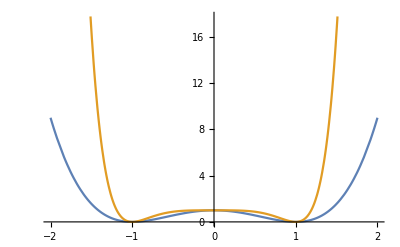

```mathematica
Plot[{(x^2-1)^2,(x^4-1)^2},{x,-2,2}]
```

```mathematica
term=a(x^2-1)^2+b(x^4-1)^2//Expand//Simplify
```

(-1+x^2)^2 (a+b (1+x^2)^2)